```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
dataPascal = Drop[Import[NotebookDirectory[]<>"2x2_out_all.dat"],7];
dataPascal = Transpose[{Transpose[dataPascal][[1]], Transpose[dataPascal][[2]],Transpose[dataPascal][[3]]}];
```

Import::nffil: File not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed,7].

Part::partw: Part 2 of Transpose[Drop[$Failed,7]] does not exist.

Part::partw: Part 3 of Transpose[Drop[$Failed,7]] does not exist.

Transpose::nmtx: The first two levels of {Drop[$Failed,7],Transpose[Drop[$Failed,7]]⟦2⟧,Transpose[Drop[$Failed,7]]⟦3⟧} cannot be transposed.

```mathematica
(*Compl. dom*)
Z0 =  872/9 + 2320*(2m)^2/3 + 1303*(2m)^4 + 624*(2m)^6 + (2m)^8*72;
(*Only 1 bag of size 1*)
Z1 =872/9 + 2320*(2m)^2/3 + 1303*(2m)^4 + 624*(2m)^6 + (2m)^8*72  + 160(2m)^6 + 96(2m)^8;
(*No 2x2 bags*)
Z2 =  872/9 + 2320*(2m)^2/3 + 1303*(2m)^4 + 624*(2m)^6 + (2m)^8*72  + 160(2m)^6 + 96(2m)^8 + ((2m)^6+4)(20(2m)^2 + 12(2m)^4 + 4) + ((2m)^6)(20(2m)^2 + 12(2m)^4 + 4);
(*2 Site bag and 4 site bag*)
Z24 = 872/9 + 2320*(2m)^2/3 + 1303*(2m)^4 + 624*(2m)^6 + (2m)^8*72  +  ((2m)^6  + 4 )(4 + 20(2m)^2 + 12(2m)^4) + (2m)^6 (4 + 20(2m)^2 + 12(2m)^4)  + 16 +(2m)^12 + 8(2m)^6;
 (*Full*)
Zf = 8/9 (145+6 m^2 (640+4053 m^2+384 m^4 (25+2 m^2 (13+6 m^2+m^4))));
```

```mathematica
cond0 = D[Log[Z0],m]/8;
cond1 = D[Log[Z1],m]/8;
cond2 = D[Log[Z2],m]/8;
cond24 = D[Log[Z24],m]/8;
condf = D[Log[Zf],m]/8;
```

```mathematica
condf/.m-> 1.0//Simplify
```

0.885614

```mathematica
mmin = 0;
mmax = 10;
```

```mathematica
p1 = Plot[cond0, {m, mmin, mmax}, PlotStyle->{Dashed, Orange}];
p2 = Plot[cond1, {m, mmin, mmax}, PlotStyle->{Dashed, Orange}];
p3 = Plot[cond2, {m, mmin, mmax}, PlotStyle->{Dashed, Orange}];
p4 = Plot[cond24, {m, mmin, mmax}, PlotStyle->{Dashed, Orange}];
p5 = Plot[condf, {m, mmin, mmax}, PlotStyle->{Dashed, Orange}];
```

```mathematica
data0 = Import[NotebookDirectory[]<>"cond0_data.dat"];
data1 = Import[NotebookDirectory[]<>"cond1_data.dat"];
data2 = Import[NotebookDirectory[]<>"cond2_data.dat"];
data24 = Import[NotebookDirectory[]<>"cond24_data.dat"];
dataf = Import[NotebookDirectory[]<>"condf_data.dat"];
```

Import::nffil: File not found during Import.

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[$Failed,{},Method→{OptimizePlotMarkers→False}]].

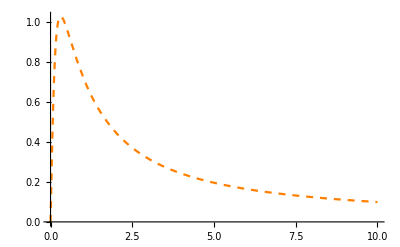
Show[-Graphics-,ListPlot[$Failed,{},Method→{OptimizePlotMarkers→False}]]

```mathematica
Show[p1, ErrorListPlot[data0]]
```

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[$Failed,{},Method→{OptimizePlotMarkers→False}]].

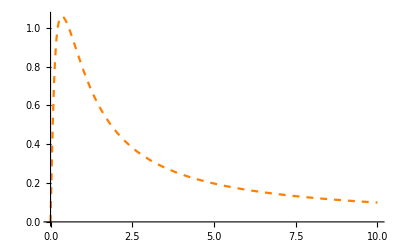
Show[-Graphics-,ListPlot[$Failed,{},Method→{OptimizePlotMarkers→False}]]

```mathematica
Show[p2, ErrorListPlot[data1]]
```

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[$Failed,{},Method→{OptimizePlotMarkers→False}]].

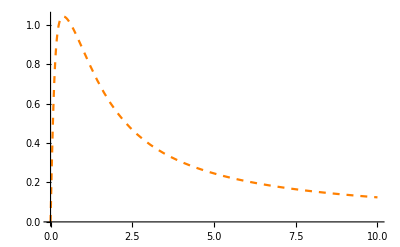
Show[-Graphics-,ListPlot[$Failed,{},Method→{OptimizePlotMarkers→False}]]

```mathematica
Show[p3, ErrorListPlot[data2]]
```

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

ListPlot::lpn: dataBB24 is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in Show[,ListPlot[$Failed,{},Method→{OptimizePlotMarkers→False}],ListPlot[dataBB24,{},Method→{OptimizePlotMarkers→False}]].

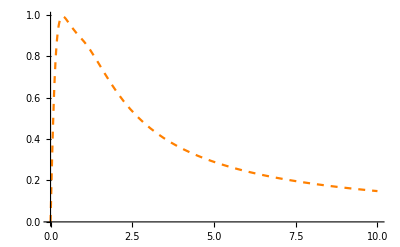
Show[-Graphics-,ListPlot[$Failed,{},Method→{OptimizePlotMarkers→False}],ListPlot[dataBB24,{},Method→{OptimizePlotMarkers→False}]]

```mathematica
Show[p4, ErrorListPlot[data24], ErrorListPlot[dataBB24]]
```

ListPlot::lpn: Transpose[{Drop[$Failed,7],Transpose[Drop[$Failed,7]]⟦2⟧,Transpose[Drop[$Failed,7]]⟦3⟧}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

General::sfunc: {{Identity,Identity},{Identity,Identity}} is not a valid scaling function.

General::stop: Further output of General::sfunc will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

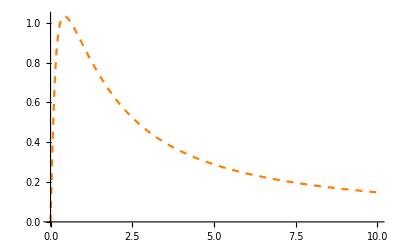
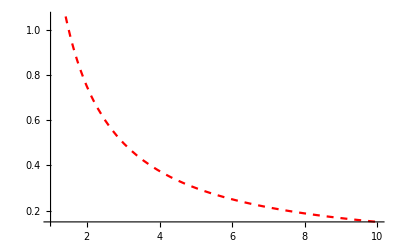
Show[-Graphics-,ListPlot[Transpose[{Drop[$Failed,7],Transpose[Drop[$Failed,7]]⟦2⟧,Transpose[Drop[$Failed,7]]⟦3⟧}],{PlotStyle→RGBColor[0, 1, 0]},Method→{OptimizePlotMarkers→False}],ListPlot[$Failed,{},Method→{OptimizePlotMarkers→False}],-Graphics-,PlotRange→All]

```mathematica
Show[p5, ErrorListPlot[dataPascal, PlotStyle->Green], ErrorListPlot[dataf], Plot[3/(2m), {m, 1, 10}, PlotStyle->{Dashed, Red}],PlotRange->All]
```

```mathematica
Zf/3//FullSimplify
```

8/27 (145+6 m^2 (640+4053 m^2+384 m^4 (25+2 m^2 (13+6 m^2+m^4))))

```mathematica
dataBB24 = Import["/home/oliver/Documents/Work/BaryonBags/Code/cond_data.dat"]
```

{{0.02,0.489834,0.00119031},{0.04,0.82679,0.00100418},{0.06,0.986667,0.000834119},{0.08,1.07269,0.000715587},{0.1,1.11913,0.000633114},{0.12,1.14305,0.0005717}}

```mathematica
ZZf =  872/9 + 2320*(2m)^2/3 + 1303*(2m)^4 + 624*(2m)^6 + (2m)^8*72  + 160(2m)^6 + 96(2m)^8 + ((2m)^6  + 4 )(4 + 20(2m)^2 + 12(2m)^4) + (2m)^6 (4 + 20(2m)^2 + 12(2m)^4)  + 16 +(2m)^12 + 8(2m)^6;
```

```mathematica
BagSize = (160(2m)^6 + 96(2m)^8 + 2*(((2m)^6  + 4 )(4 + 20(2m)^2 + 12(2m)^4) + (2m)^6 (4 + 20(2m)^2 + 12(2m)^4))  + 4*(16 +(2m)^12 + 8(2m)^6))/ZZf;
```

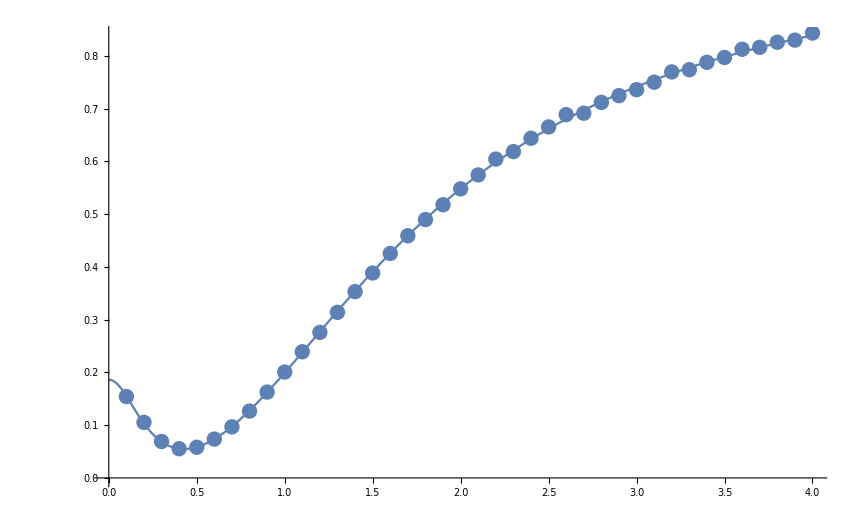

```mathematica
Show[Plot[BagSize, {m, 0, 4}], ErrorListPlot[data]]
```

```mathematica
data = Import["/home/oliver/Documents/Work/4by4_BaryonBags/T_Code_varm/10t_2x2_bag_size_stats.dat"];
```

```mathematica
SBList = Table[N[{m,  N[BagSize,50]}], {m, 0.4, 0.5, 1/100000}]
```

{{0.4,0.055434},{0.40001,0.0554335},{0.40002,0.0554331},{0.40003,0.0554327},{0.40004,0.0554323},9992,{0.49997,0.0585197},{0.49998,0.0585206},{0.49999,0.0585216},{0.5,0.0585226}}
 |  |  |  |

```mathematica
(*Export["SU(3)_bag_size_counted.dat", SBList]*)
```

```mathematica
BagSus = D[BagSize, m]/2;
CondSus = D[condf, m];
```

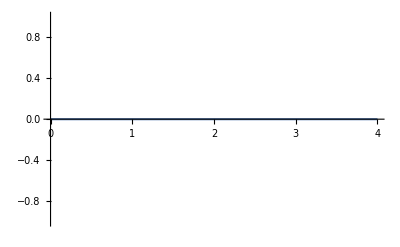

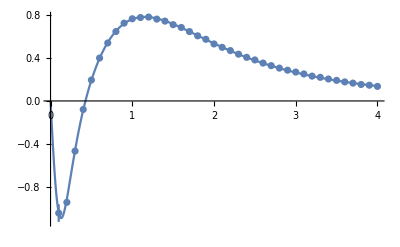

```mathematica
Plot[CondSus, {m,0,4}, PlotRange->All]
Show[Plot[BagSus, {m,0,4}], ErrorListPlot[dataSBsus], PlotRange->All]
```

```mathematica
dataSBsus = 
Import["/home/oliver/Documents/Work/4by4_BaryonBags/T_Code_varm/10t_2x2_bag_size_susc.dat"]
```

{{0.1,-1.04793,0.0823425},{0.2,-0.947386,0.00236375},{0.3,-0.468233,0.00189921},{0.4,-0.0796767,0.00310836},{0.5,0.195567,0.00119457},{0.6,0.400871,0.00486944},{0.7,0.541671,0.000933531},{0.8,0.648467,0.0213141},{0.9,0.727298,0.00869717},{1,0.768097,0.00684705},{1.1,0.779599,0.00700492},{1.2,0.784021,0.00557927},{1.3,0.764926,0.00182986},{1.4,0.746092,0.00380219},{1.5,0.712879,0.00397656},{1.6,0.6866,0.00319323},{1.7,0.648242,0.00745712},{1.8,0.60857,0.00426313},{1.9,0.576337,0.00423088},{2,0.532724,0.00381633},{2.1,0.501029,0.00217037},{2.2,0.470661,0.0013386},{2.3,0.437015,0.00200229},{2.4,0.40758,0.00256315},{2.5,0.383246,0.00225447},{2.6,0.353966,0.000139208},{2.7,0.329989,0.000114876},{2.8,0.307073,0.000317445},{2.9,0.287494,0.00116568},{3,0.270011,0.0009678},{3.1,0.252164,0.00486612},{3.2,0.232135,0.000449981},{3.3,0.220706,0.000358096},{3.4,0.20521,0.000647566},{3.5,0.192402,0.000647034},{3.6,0.177767,0.000216103},{3.7,0.166677,0.000629853},{3.8,0.153907,0.000440787},{3.9,0.147156,0.000490443},{4,0.136077,0.000595046}}

```mathematica
SBSusList = Table[N[{m,  N[BagSus,50]}], {m, 0.0, 4, 1/1000}]
```

{{0.,0.},{0.001,-0.014759},{0.002,-0.0295147},{0.003,-0.0442637},{0.004,-0.0590027},{0.005,-0.0737284},3990,{3.996,0.138949},{3.997,0.138865},{3.998,0.13878},{3.999,0.138696},{4.,0.138611}}
 |  |  |  |

```mathematica
(*Export["SU(3)_bag_size_sus_counted.dat", SBSusList]*)
```

SU(3)_bag_size_sus_counted.dat